```mathematica
opencldirectory="/home/chris/Programming/GPU/opencl3/";
```

```mathematica
NotebookEvaluate[opencldirectory<>"DetectPeriodTools2.wl"]
NotebookEvaluate[opencldirectory<>"build.wl"]
```

```mathematica
Clear[ProgressMap]
ProgressMap[f_, l_List]:=Module[{stdout=PrintTemporary[""], len=Length[l], begin=TimeObject[], cur, avg,eta, tmp, cont=True, out, i=0},
out=ConstantArray[0, len];
While[cont,
i++;
out[[i]]=f[l[[i]]];
NotebookDelete[stdout];
cur=TimeObject[];avg=(cur-begin)/i;eta=begin+len*avg;stdout=PrintTemporary["Step "<>ToString[i]<>"/"<>ToString[len]<>" ("<>ToString[N[100*i/len]]<>"% complete, Avg Time "<>ToString[QuantityMagnitude[avg,"Seconds"]]<>" seconds per elem, ETA "<>DateString[eta, "DateTimeShort"]<>") ", Button["Stop", cont=False]]; 
If[i>=len, cont=False];
];
out[[;;i]]
]
ProgressMap[f_, l_Integer]:=ProgressMap[f, ConstantArray[0, l]]
```

```mathematica
colors=Table[Hue[i], {i, 0, 2Pi, 0.1}];
(* colors={Red, Green, Blue, Pink, Orange, Purple}; *)
colors[[Mod[Hash[0], Length[colors]]+1]]=White;

UniqueColor[hashable_]:=colors[[Mod[Hash[hashable], Length[colors]]+1]]
```

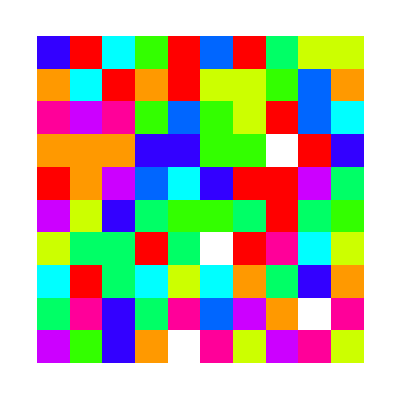

```mathematica
ArrayPlot[Table[RandomChoice[colors], {i, 10}, {j, 10}]]
```

```mathematica
n=2;
Thread[HilbertCurve[n][[1]]->Table[i,{i, 4^n}]]
```

{{0,0}→1,{1,0}→2,{1,1}→3,{0,1}→4,{0,2}→5,{0,3}→6,{1,3}→7,{1,2}→8,{2,2}→9,{2,3}→10,{3,3}→11,{3,2}→12,{3,1}→13,{2,1}→14,{2,0}→15,{3,0}→16}

```mathematica
i=195;
Min[Join[#, Reverse[#]]&[FromDigits[#, 2]&/@FindRepeatDeterministicByStripZeros[RunCA[{20, {2, 1}, 2}, i, 100]]]]
```

15903

```mathematica
GrayCode=ResourceFunction["GrayCode"]
```

```mathematica
GrayCode[10]
```

{1,1,1,1}

```mathematica
4^9
```

262144

```mathematica
n=9;
FromRules[rules_]:=Module[{o=ConstantArray[0, {2^n, 2^n}]},
Do[o[[1+rule[[1]][[1]], 1+rule[[1]][[2]]]]=rule[[2]], {rule, rules}];
o
]

rules=Thread[HilbertCurve[n][[1]]->ParallelTable[UniqueColor@Min[Join[#, Reverse[#]]&[FromDigits[#, 2]&/@FindRepeatDeterministicByStripZeros[RunCA[{20, {2, 1}, 2}, GrayCode[i], 100]]]],{i, 1,2*4^n, 2}]];

ArrayPlot[FromRules[rules], Frame->False]
```

-Graphics-

```mathematica
ImageApply[1-3*(1-#)&, Blur[, 5]]
```

-Graphics-

```mathematica
GPUStructureSearch[{1329, {3, 1}, 1}, 0, 100000]
```

{400,1199,1211,3130,3398,3554,7199,7772,9571,9934,10420,11417,11573,12146,12607,20321,21355,22234,22960,23056,25000,25243,25729,32476,37636,38411,38444,38465,38471,38480,38486,38498,38519,38525,59687,59992,60416,61450,61693,61718,61874,62908,66067,66248,66553,66821,67282,68740,70441,70466,70622,70927,71170,71195,71656,74815,75301,85750,85931,86660,88423,88691,88847,90149,90305,90878,93040,93221,93526,94498,94679,94984,95252,95408,97114,97171,97357,97414,97427,97439,184315,266113,292070,20990041,27598819,525304562024518979,880853240277422984}

```mathematica
n=9;
FromRules[rules_]:=Module[{o=ConstantArray[0, {2^n, 2^n}]},
Do[o[[1+rule[[1]][[1]], 1+rule[[1]][[2]]]]=rule[[2]], {rule, rules}];
o
]

rules=Thread[HilbertCurve[n][[1]]->ParallelTable[UniqueColor@Min[Join[#, Reverse[#]]&[FromDigits[#, 3]&/@FindRepeatDeterministicByStripZeros[RunCA[{1329, {3, 1}, 1}, i, 100]]]],{i, 1,2*4^n, 2}]];

ArrayPlot[FromRules[rules], Frame->False]
```

-Graphics-

```mathematica
IntegerName[3065255504688667359757]
```

3 sextillion 65 quintillion 255 quadrillion 504 trillion 688 billion 667 million 359 thousand 757

```mathematica
AArrayPlot[{1329, {3, 1}, 1}, RandomInteger[4^9], 1000]
```

-Graphics-

```mathematica
ResourceFunction["GrayCodeSubsets"]
```

```mathematica
ClickToCopy[AArrayPlot[{1329, {3, 1}, 1}, #, 1000], #]&/@
```

{-Graphics-400,-Graphics-1199,-Graphics-1211,-Graphics-3130,-Graphics-3398,-Graphics-3554,-Graphics-7199,-Graphics-7772,-Graphics-9571,-Graphics-9934,-Graphics-10420,-Graphics-11417,-Graphics-11573,-Graphics-12146,-Graphics-12607,-Graphics-20321,-Graphics-21355,-Graphics-22234,-Graphics-22960,-Graphics-23056,-Graphics-25000,-Graphics-25243,-Graphics-25729,-Graphics-32476,-Graphics-37636,-Graphics-38411,-Graphics-38444,-Graphics-38465,-Graphics-38471,-Graphics-38480,-Graphics-38486,-Graphics-38498,-Graphics-38519,-Graphics-38525,-Graphics-59687,-Graphics-59992,-Graphics-60416,-Graphics-61450,-Graphics-61693,-Graphics-61718,-Graphics-61874,-Graphics-62908,-Graphics-66067,-Graphics-66248,-Graphics-66553,-Graphics-66821,-Graphics-67282,-Graphics-68740,-Graphics-70441,-Graphics-70466,-Graphics-70622,-Graphics-70927,-Graphics-71170,-Graphics-71195,-Graphics-71656,-Graphics-74815,-Graphics-75301,-Graphics-85750,-Graphics-85931,-Graphics-86660,-Graphics-88423,-Graphics-88691,-Graphics-88847,-Graphics-90149,-Graphics-90305,-Graphics-90878,-Graphics-93040,-Graphics-93221,-Graphics-93526,-Graphics-94498,-Graphics-94679,-Graphics-94984,-Graphics-95252,-Graphics-95408,-Graphics-97114,-Graphics-97171,-Graphics-97357,-Graphics-97414,-Graphics-97427,-Graphics-97439,-Graphics-184315,-Graphics-266113,-Graphics-292070,-Graphics-20990041,-Graphics-27598819,-Graphics-525304562024518979,-Graphics-880853240277422984}

```mathematica
AArrayPlot[{1329, {3, 1}, 1}, 1211, 1000, Frame->False]
```

-Graphics-

```mathematica
FromDigits[{1, 1, 1, 0, 1, 0, 0, 1}, 2]
```

233

```mathematica
DedupSame@DetectPeriod[{1329, {3, 1}, 1}, 1211]
```

{<|Rule→{1329,{3,1},1},Canonical→525304562024518979,Original→1211,IsGliderGun→False,MaxDepth→4,MaxSteps→6200,Period→48,Shift→24,LowestDepth→16|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→1211,IsGliderGun→False,MaxDepth→3,MaxSteps→3000,Period→78,Shift→0,LowestDepth→17|>}

```mathematica
ToString[{<|"Rule"->{1329,{3,1},1},"Canonical"->525304562024518979,"Original"->1211,"IsGliderGun"->False,"MaxDepth"->4,"MaxSteps"->6200,"Period"->48,"Shift"->24,"LowestDepth"->16|>,<|"Rule"->{1329,{3,1},1},"Canonical"->9571,"Original"->1211,"IsGliderGun"->False,"MaxDepth"->3,"MaxSteps"->3000,"Period"->78,"Shift"->0,"LowestDepth"->17|>}]
```

{<|Rule -> {1329, {3, 1}, 1}, Canonical -> 525304562024518979, Original -> 1211, IsGliderGun -> False, MaxDepth -> 4, MaxSteps -> 6200, Period -> 48, Shift -> 24, LowestDepth -> 16|>, <|Rule -> {1329, {3, 1}, 1}, Canonical -> 9571, Original -> 1211, IsGliderGun -> False, MaxDepth -> 3, MaxSteps -> 3000, Period -> 78, Shift -> 0, LowestDepth -> 17|>}

```mathematica
StringReplace[, {" "->"", "\n"->""}]
```

{<|Rule->{1329,{3,1},1},Canonical->525304562024518979,Original->1211,IsGliderGun->False,MaxDepth->4,MaxSteps->6200,Period->48,Shift->24,LowestDepth->16|>,<|Rule->{1329,{3,1},1},Canonical->9571,Original->1211,IsGliderGun->False,MaxDepth->3,MaxSteps->3000,Period->78,Shift->0,LowestDepth->17|>}

```mathematica
GPUStructureSearch[{20, {2, 1}, 2}, 0, 1000000000]
```

{151,187,189,221,635,889,15903,125231,595703,610999,624623,14871103,16537415,22503642597}

```mathematica
rule={20, {2, 1}, 2};
AbsoluteTiming[DedupSame[Catenate[Table[DetectPeriod[rule,i],{i,1,10000}]]]]
```

{2.17349,{<|Rule→{20,{2,1},2},Canonical→189,Original→189,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→635,Original→635,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→1,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→151,Original→151,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→2,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→187,Original→187,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→9,Shift→1,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→15903,Original→195,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→22,Shift→0,LowestDepth→20|>}}

```mathematica
[[1]]/10000
```

0.000217349

```mathematica
UnitConvert[Quantity[, "Seconds"], "Microseconds"]
```

217.349 μs

```mathematica
rule={1329, {3, 1}, 1};
AbsoluteTiming[DedupSame[Catenate[Table[DetectPeriod[rule,i],{i,1,1000}]]]]
```

{1.32327,{<|Rule→{1329,{3,1},1},Canonical→400,Original→400,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→2,Shift→0,LowestDepth→20|>,<|Rule→{1329,{3,1},1},Canonical→22960,Original→52,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→7,Shift→0,LowestDepth→20|>,<|Rule→{1329,{3,1},1},Canonical→22234,Original→800,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→12,Shift→0,LowestDepth→20|>,<|Rule→{1329,{3,1},1},Canonical→20990041,Original→916,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→31,Shift→7,LowestDepth→20|>,<|Rule→{1329,{3,1},1},Canonical→525304562024518979,Original→457,IsGliderGun→False,MaxDepth→3,MaxSteps→3000,Period→48,Shift→24,LowestDepth→17|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→1,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→78,Shift→0,LowestDepth→20|>}}

```mathematica
[[1]]/1000
```

0.00132327

```mathematica
UnitConvert[Quantity[, "Seconds"], "Microseconds"]
```

1323.27 μs

```mathematica
rule={20, {2, 1}, 2};
AbsoluteTiming[DedupSame[Catenate[ParallelTable[DetectPeriod[rule,i],{i,1,1000000}]]]]
```

$Aborted